## Basic Functions :

```mathematica
ClearAll["Global`*"]
```

### Basic Definitions :

```mathematica
(*Parallel Energy*)
Ekp[M_,pz_]:=Sqrt[M^2+pz^2];

(*Total Energy*)
Ekr[px_,py_,pz_,q_,M_,r_]:=Sqrt[px^2+py^2+pz^2+q^2/4+M^2+(-1)^(r-1)*q*Ekp[M,pz]];
```

### Plotting Variables :

#### Distribution Functions :

```mathematica
fkrFD[px_,py_,pz_,q_,M_,T_,r_,mu_]:=1/(Exp[Ekr[px,py,pz,q,M,r]/T-mu/T]+1);
afkrFD[px_,py_,pz_,q_,M_,T_,r_,mu_]:=1/(Exp[Ekr[px,py,pz,q,M,r]/T+mu/T]+1);
```

#### INTEGRANDS :

```mathematica
(*A^3 Integrand*)
InA3FD[px_,py_,pz_,q_,M_,T_,r_,mu_]:=(((-1)^r*Ekp[M,pz])/Ekr[px,py,pz,q,M,r])*(1+((-1)^(r-1)*q)/(2*Ekp[M,pz]))*(fkrFD[px,py,pz,q,M,T,r,mu]+afkrFD[px,py,pz,q,M,T,r,mu]);
```

#### INTEGRALS :

```mathematica
(*A^3(x)- Definition*)
A3FD[q_,M_,T_,mu_]:=NIntegrate[Sum[InA3FD[px,py,pz,q,M,T,r,mu],{r,1,2}],{pz,-∞,∞},{py,-∞,∞},{px,-∞,∞},AccuracyGoal->15,Method->{"LocalAdaptive"}];
```

## Results :

```mathematica
LaunchKernels[];
DistributeDefinitions[Ekp,Ekr,fkrFD,afkrFD,InA3FD,A3FD];
```

```mathematica
(*Timing[qA3FDM321=ParallelTable[{i,1.A3FD[i,0.001,0.5,0.1],1. A3FD[i,0.01,0.5,0.1],1. A3FD[i,0.1,0.5,0.1]},{i,0.1,0.5,0.0001}]]//Quiet;*)
```

```mathematica
Timing[qA3FDM321v2=ParallelTable[{i,1.A3FD[i,0.01,0.5,0.1],1. A3FD[i,0.1,0.5,0.1],1. A3FD[i,1,0.5,0.1]},{i,0.1,0.5,0.001}]]//Quiet;
```

```mathematica
qM135=qA3FDM135=ParallelTable[{i,1.A3FD[i,0.1,0.15,0.1],1. A3FD[i,0.3,0.15,0.1],1. A3FD[i,0.5,0.15,0.1]},{i,0.1,0.5,0.001}]//Quiet;
```

```mathematica
qM345=qA3FDM345=ParallelTable[{i,1.A3FD[i,0.3,0.15,0.1],1. A3FD[i,0.4,0.15,0.1],1. A3FD[i,0.5,0.15,0.1]},{i,0,0.3,0.001}]//Quiet;
```

```mathematica
Timing[μA3FDM321v2=ParallelTable[{i,1.A3FD[0.1,0.01,0.5,i],1. A3FD[0.1,0.1,0.5,i],1. A3FD[0.1,1,0.5,i]},{i,0.1,5,0.005}]]//Quiet;
```

```mathematica
Timing[μA3FDM321v1=ParallelTable[{i,1.A3FD[0.1,0.01,0.5,i],1. A3FD[0.1,0.1,0.5,i],1. A3FD[0.1,1,0.5,i]},{i,0.1,5,0.1}]]//Quiet;
```

```mathematica
Timing[μA3FDM135=ParallelTable[{i,1.A3FD[0.1,0.1,0.15,i],1. A3FD[0.1,0.3,0.15,i],1. A3FD[0.1,0.5,0.15,i]},{i,0.1,5,0.01}]]//Quiet;
μA3FDM345=ParallelTable[{i,1.A3FD[0.1,0.3,0.15,i],1. A3FD[0.1,0.4,0.15,i],1. A3FD[0.1,0.5,0.15,i]},{i,0.1,5,0.01}]//Quiet;
```

```mathematica
μA3FDM345v2=ParallelTable[{i,1.A3FD[0.1,0.3,0.15,i],1. A3FD[0.1,0.4,0.15,i],1. A3FD[0.1,0.5,0.15,i]},{i,0.01,0.5,0.001}]//Quiet;
```

```mathematica
μA3FDT123=ParallelTable[{i,1.A3FD[0.1,0.3,0.15,i],1. A3FD[0.1,0.3,0.3,i],1. A3FD[0.1,0.3,0.45,i]},{i,0,0.5,0.001}]//Quiet;
```

```mathematica
Timing[MA3FDT123=ParallelTable[{i,1.A3FD[0.1,i,0.15,0.1],1. A3FD[0.1,i,0.3,0.1],1. A3FD[0.1,i,0.45,0.1]},{i,0.1,5,0.1}]]//Quiet;
```

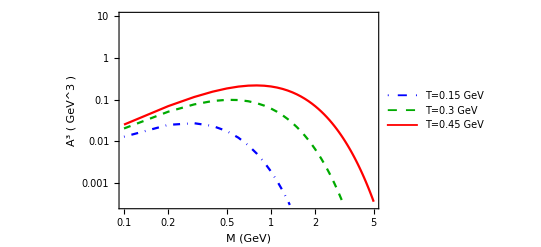
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogLogPlot[{MA3FDT123[[All,{1,2}]],MA3FDT123[[All,{1,3}]],MA3FDT123[[All,{1,4}]]},
GridLines->{{0.2,0.5,1,2,5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,5},{0.0003,10}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["M   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*T=0.15 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*T=0.3 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*T=0.45 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

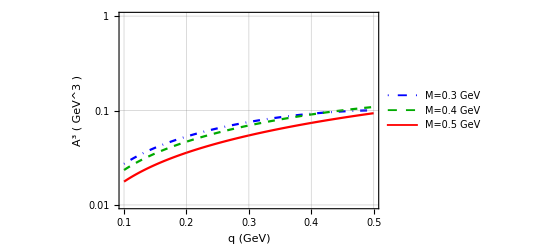
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogPlot[{qA3FDM345[[All,{1,2}]],qA3FDM345[[All,{1,3}]],qA3FDM345[[All,{1,4}]]},
GridLines->{{0.1,0.2,0.3,0.4,0.5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,0.5},{0.01,1}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["q   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.3 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.4 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.5 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

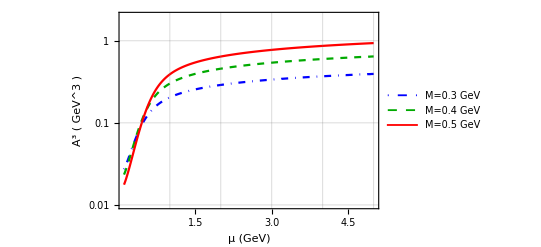
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogPlot[{μA3FDM345[[All,{1,2}]],μA3FDM345[[All,{1,3}]],μA3FDM345[[All,{1,4}]]},
GridLines->{{1,2,3,4,5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,5},{0.01,2}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["μ   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.3 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.4 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.5 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

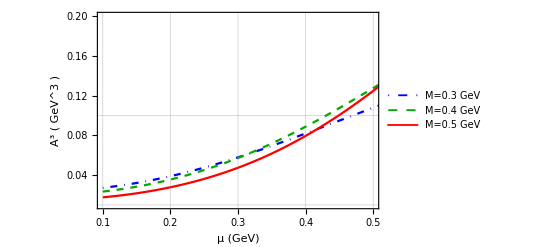
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListPlot[{μA3FDM345[[All,{1,2}]],μA3FDM345[[All,{1,3}]],μA3FDM345[[All,{1,4}]]},
GridLines->{{0.1,0.2,0.3,0.4,0.5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,0.5},{0.01,0.2}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["μ   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.3 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.4 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.5 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

```mathematica
(*Labeled[
ListLogPlot[{qA3FDM321[[All,{1,2}]],qA3FDM321[[All,{1,3}]],qA3FDM321[[All,{1,4}]]},
GridLines->{{0.1,0.2,0.3,0.4,0.5},{0,0.00001,0.0001,0.001,0.01}},Joined->True,Frame->True,PlotRange->Automatic,PlotTheme->"Scientific",PlotStyle->{{Blue,Dashed,Thickness[0.003]},{Darker[Green],DotDashed,Thickness[0.0035]},{Red,Thickness[0.003]}},
FrameLabel->{Style[HoldForm["q   (GeV)"],16],Style[HoldForm[SuperscriptBox["A","3"]//DisplayForm],14]},PlotLegends->Placed[LineLegend[{"M=0.001 GeV","M=0.01 GeV","M=0.1 GeV"},LegendFunction->(Framed[#, FrameMargins -> 0,RoundingRadius->4,Background->RGBColor[.95,.95,.95,1]] & )],{0.7,0.5}]],{Bottom,Left},RotateLabel->True]*)
```

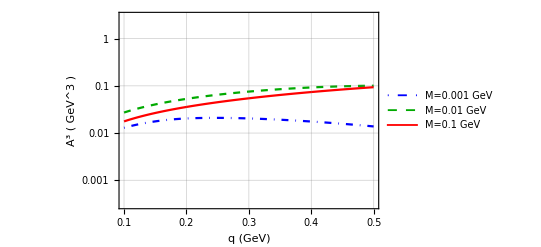
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogPlot[{qA3FDM135[[All,{1,2}]],qA3FDM135[[All,{1,3}]],qA3FDM135[[All,{1,4}]]},
GridLines->{{0.1,0.2,0.3,0.4,0.5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,0.5},{0.0003,3}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["q   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.001 GeV\)",12,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.01 GeV\)",12,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.1 GeV\)",12,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->Function[{x},Grid[x,Spacings->{0.6,0},Alignment->Left]],LegendMarkerSize->{22,12},LegendFunction->(Framed[#,FrameStyle->Directive[Thickness[0.5]],RoundingRadius->4,Background->RGBColor[0.98,0.98,0.98,1]]&)],{0.77,0.35}]],{Bottom,Left},RotateLabel->True]
```

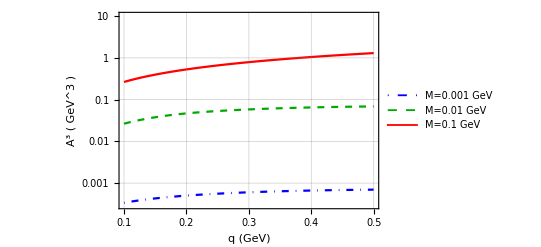
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogPlot[{qA3FDM321v2[[All,{1,2}]],qA3FDM321v2[[All,{1,3}]],qA3FDM321v2[[All,{1,4}]]},
GridLines->{{0.1,0.2,0.3,0.4,0.5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,0.5},{0.0003,10}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["q   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.001 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.01 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.1 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

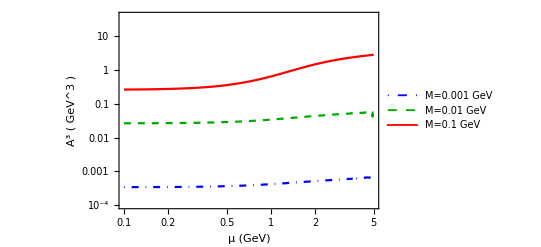
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogLogPlot[{μA3FDM321v1[[All,{1,2}]],μA3FDM321v2[[All,{1,3}]],μA3FDM321v2[[All,{1,4}]]},
GridLines->{{0.2,0.5,1,2,5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,5},{0.0001,40}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["μ   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.001 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.01 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.1 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

```mathematica
Labeled[
ListLogLogPlot[{μA3FDM321v1[[All,{1,2}]],μA3FDM321v2[[All,{1,3}]],μA3FDM321v2[[All,{1,4}]]},
GridLines->{{0.2,0.5,1,2,5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,5},{0.0001,40}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["μ   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.001 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.01 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.1 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

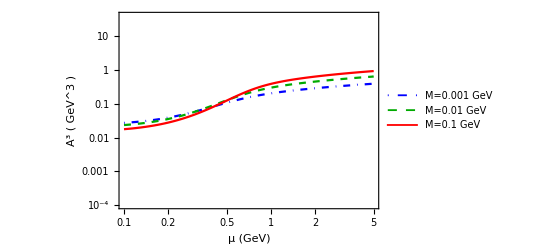
-Graphics-{Bottom,Left}

```mathematica
Labeled[
ListLogLogPlot[{μA3FDM345[[All,{1,2}]],μA3FDM345[[All,{1,3}]],μA3FDM345[[All,{1,4}]]},
GridLines->{{0.2,0.5,1,2,5},{0,0.001,0.01,0.1,1}},Joined->True,Frame->True,PlotRange->{{0.1,5},{0.0001,40}},PlotTheme->"Scientific",PlotStyle->{{Blue,DotDashed,Thickness[0.004]},{Darker[Green],Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},
FrameLabel->{Style[HoldForm["μ   (GeV)"],16,FontSlant->Italic],Style[HoldForm[SuperscriptBox["A","3"] "("SuperscriptBox["GeV"," 3"]")"//DisplayForm],14,FontSlant->Italic]},PlotLegends->Placed[LineLegend[{Style["\!\(\*M=0.001 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p⃗=0(r=2)\)",8]*),
Style["\!\(\*M=0.01 GeV\)",10.5,FontFamily->Times,FontSlant->Italic],(*Style["\!\(\*p_⊥=0,p^3=M(r=2)\)",8],*)
Style["\!\(\*M=0.1 GeV\)",10.5,FontFamily->Times,FontSlant->Italic](*,Style["\!\(\*p_⊥=p^3=M(r=2)\)",8]*)},LegendLayout->{"Row",1},LegendMarkerSize->{22,12}],{0.5,0.9}]],{Bottom,Left},RotateLabel->True]
```

```mathematica
Export["G:/My Drive/My Projects/2 - NJL Spin/Plots/Spin Density/qM135.dat",qM135,"Table"]
```

G:/My Drive/My Projects/2 - NJL Spin/Plots/Spin Density/qM135.dat

```mathematica
Export["G:/My Drive/My Projects/2 - NJL Spin/Plots/Spin Density/qM135csv.csv",qM135,"CSV"]
```

G:/My Drive/My Projects/2 - NJL Spin/Plots/Spin Density/qM135csv.csv

```mathematica
Export["C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/qM345csv.csv",qM345,"CSV"]
```

C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/qM345csv.csv

```mathematica
Export["C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/muM345csv.csv",μA3FDM345v2,"CSV"]
```

C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/muM345csv.csv

```mathematica
Export["C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/muT123csv.csv",μA3FDT123,"CSV"]
```

C:/Users/BHADURYS/Documents/Programming/Work/Python/NJL/Plots/muT123csv.csv